## Diffusion in One Dimension

## Completed and Analyzed in class, April 18, 2025

This is our twentieth notebook. In the last two we re-did guitar strings and drumheads using Mathematica’s ability to solve wave equations.

Now I want to introduce you to a very different kind of problem, but one which has a lot of the same mathematics as wave equations. The problem is diffusion. An example would be, how does heat distribute itself through a piece of metal?

-Graphics-

### Diffusion — Theory

The fundamental idea of diffusion is concentration differences, and random motion that tends (on average) to even out such differences.

Consider a one-dimensional rod and let’s have what is being diffused be heat energy. To model this, I might break the rod up into chunks of length a, and if the chunks are sufficiently small, I can assign a temperature to each of the chunks. (Smallness is important because if a chunk is too big, assigning a temperature to the whole chunk might not be a good approximation because the temperature might vary significantly over the size of the chunk.)

In a one-dimensional chunk, if we assign an integer j to the chunk, then the chunk to the right of it might have integer j+1 and the chunk to the left j-1. There will be a temperature in each chunk: T_(j-1), T_j, and T_(j+1).

Now for a big assumption: the amount of heat flowing from into chunk j from the left is some proportionality constant times the temperature difference:

σ (T_(j-1)-T_j)

The amount of heat flowing from into chunk j from the right is some proportionality constant times the temperature difference (let’s have the one-dimensional rod be uniform, the consequence of which is that the proportionality constant is the same:

σ (T_(j+1)-T_j)

So the total heat flowing into chunk j is:

σ (T_(j-1)-T_j)+σ (T_(j+1)-T_j)=σ(T_(j+1)+T_(j-1)-2 T_j)

Maybe this is already starting to look suspiciously similar to the one-dimensional wave problem!

As heat flows in to chunk j, it raises its temperature. A fundamental and simplifying assumption (that can be made a little more general) is that the temperature increase is proportional to the heat flow. The coefficient of proportionality is called the “specific heat,” and our symbol for that will be c, so our formula is:

c dT/dt=σ(T_(j+1)+T_(j-1)-2 T_j)

As the size of the chunks goes to zero the right-hand side becomes the second derivative with respect to the position, x, along the rod, and so we have:

c dT/dt=σ(d^2 T)/(d x^2)

If you want to relax the simplifying assumptions of uniformity of the rod, and that the specific heat is just a simple constant, you get the somewhat more general equation

c(T,x) dT/dt=σ(x)(d^2 T)/(d x^2)

Regardless of whether c(T,x) and  σ(x) are constants or functions, they are prescribed. The only function we are having Mathematica find for us is T(t,x).

### The Diffusion Differential Equation

Let’s do the case of constant c and constant σ. It isn’t very hard, but it already lets us see what solutions are going to look like. Recopying:

c dT/dt=σ(d^2 T)/(d x^2)

Review the guitar string notebook if you need to be reminded how we specified the partial differential equation to Mathematica. I chose the constants so c/σ=100 which slows down the approach to equilibrium:

```mathematica
Module[{c=10, sigma=1/10},{ c Derivative[1,0][temp][t,x]==sigma Derivative[0,2][temp][t,x]}] // TraditionalForm
```

{temp^(1,0)(t,x)==temp^(0,2)(t,x)}

### Adding the Boundary Conditions

Let’s give the rod a length and hold one end of it in the forge at some high temperature and the other end in an ice bath. Our boundary conditions are then:

```mathematica
length=1;
forgeTemp=1000;
iceBathTemp=0;

Module[{c=10, sigma=1/10 },{ c Derivative[1,0][temp][t,x]==sigma Derivative[0,2][temp][t,x],temp[t,0]==forgeTemp,temp[t,length]==iceBathTemp}] // TraditionalForm
```

{10 temp^(1,0)(t,x)==1/10 temp^(0,2)(t,x),temp(t,0)==1000,temp(t,1)==0}

### Adding the Initial Conditions

The rod might be quite non-uniformly heated at t=0. The interesting thing is then, how will the heat diffuse along the rod. Let’s try a jagged initial function:

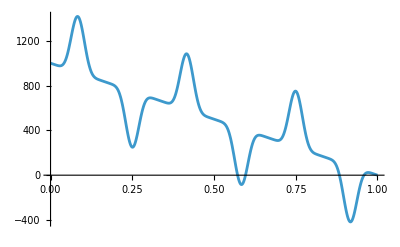

```mathematica
numberOfJaggies=6;
amplitudeOfJaggies=500;
lengthOfJaggies=length/numberOfJaggies;
f[x_]:=amplitudeOfJaggies Sin[(Pi x)/lengthOfJaggies]^7+forgeTemp+ (iceBathTemp-forgeTemp)x/length

Plot[f[x],{x,0,length}]
```

```mathematica
oneDimensionalDiffusionProblem=Module[{c=10, sigma=1/10 },{ c Derivative[1,0][temp][t,x]==sigma Derivative[0,2][temp][t,x],temp[t,0]==forgeTemp,temp[t,length]==iceBathTemp,temp[0,x]==f[x]}]
```

{10 temp^(1,0)[t,x]==1/10 temp^(0,2)[t,x],temp[t,0]==1000,temp[t,1]==0,temp[0,x]==1000-1000 x+500 Sin[6 π x]^7}

### Making Mathematica Numerically Solve the Problem

```mathematica
oneDimensionalDiffusionSolutionRule = NDSolve[oneDimensionalDiffusionProblem,temp,{t,0,10},{x,0,length}][[1]]
```

{temp→InterpolatingFunction[{{0., 10.}, {0., 1.}}, <>]}

Convert the rule to a function:

```mathematica
oneDimensionalDiffusionSolution[t_,x_]=temp[t,x]/.oneDimensionalDiffusionSolutionRule
```

InterpolatingFunction[{{0., 10.}, {0., 1.}}, <>][t,x]

### Plotting the Numerical Solution at t=1/10

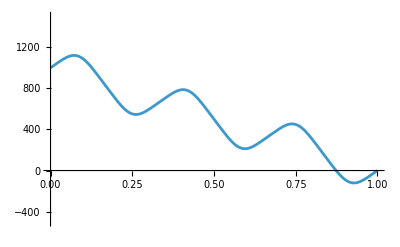

```mathematica
Plot[oneDimensionalDiffusionSolution[1/10,x],{x,0,length},PlotRange->{{0,length},{-amplitudeOfJaggies,forgeTemp+amplitudeOfJaggies}}]
```

### Animating the Numerical Solution

```mathematica
Animate[Plot[oneDimensionalDiffusionSolution[t,x],{x,0,length},PlotRange->{{0,length},{-amplitudeOfJaggies,forgeTemp+amplitudeOfJaggies}}],{t,0,1},DefaultDuration->10,AnimationRunning->False]
```

The fact that this isn’t some simple sine wave is part of what gives the guitar its tone or timber. You can exaggerate this effect by picking the string very near the bridge.